```mathematica
returnFunc[n_]:=Module[
{aRand,aSum,A,b},
aRand=RandomReal[1,{n,n}];
aSum= (aRand+Transpose[aRand])/2;
A=aSum+3 IdentityMatrix[n];
b=RandomReal[10,n];
f = Function[vec,1/2+Transpose[vec].A.vec-b.vec];
{f, A, b}
]

n=2;
plotN=100;
 
{f, A, b} =returnFunc[n];

If[
n<=1||n>=7,
Print[],
If[n==2,
Plot3D[f[{x,y}],{x,-plotN,plotN},{y,-plotN,plotN}],
If[n==3,
ContourPlot3D[f[{x,y,z}],{x,-plotN,plotN},{y,-plotN,plotN},{z,-plotN,plotN} ],
Print[]
]
]
];
```

```mathematica
heavyBall[func_,x0_,alpha_,beta_,maxIter_,tol_]:=Module[
{x,xPrev,xNew,trajectory,iter,grad,errors,h=10^-5,n=Length[x0]},numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2h),{i,n}];

xPrev=x0;
grad=numericGrad[x0];
x=x0-alpha*grad;
trajectory={xPrev,x};
errors={Norm[grad]};

For[iter=1,iter<=maxIter,iter++,
grad=numericGrad[x];
xNew=x-alpha*grad+beta*(x-xPrev);
AppendTo[errors,Norm[grad]];
AppendTo[trajectory,xNew];

If[Norm[xNew-x]<tol,
Print["Достигнута точность! Iter: ", iter];
Break[]
];
xPrev=x;
x=xNew;
];
{x,trajectory,errors}
];

nesterov[func_,x0_,alpha_,beta_,maxIter_,tol_]:=Module[
{x,xPrev,y,trajectory,iter,grad,errors,h=10^-5,n=Length[x0]},
numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2 h),{i,n}];

xPrev=x0;
x=x0;
trajectory={x0};
errors={};

For[iter=1,iter<=maxIter,iter++,
y=x+beta*(x-xPrev);
grad=numericGrad[y];
xNew=y-alpha*grad;
AppendTo[errors,Norm[grad]];
AppendTo[trajectory,xNew];

If[Norm[xNew-x]<tol,Print["Достигнута точность! Iter: ",iter];
Break[]
];
xPrev=x;
x=xNew;
];
{x,trajectory,errors}
]


conjugateGradient[func_,x0_,maxIter_,tol_]:=Module[
{x,grad,gradPrev,d,alpha, beta,trajectory,errors,iter,h=10^-5,n=Length[x0]},numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2 h),{i,n}];
x=x0;
grad=numericGrad[x];
d=-grad;
trajectory={x0};
errors={Norm[grad]};
For[iter=1,iter<=maxIter,iter++,
alpha=0.1;
x=x+alpha*d;
gradPrev=grad;
grad=numericGrad[x];
beta=(grad.grad)/(gradPrev.gradPrev);
d=-grad+beta*d;
AppendTo[trajectory,x];
AppendTo[errors,Norm[grad]];
If[Norm[grad]<tol,
Print["Достигнута точность! Iter: ",iter];
Break[]];];
{x,trajectory,errors}
]

GradientDescentNumerical[func_,initPoint_List,maxIter_,tol_]:=Module[{x=initPoint,n=Length[initPoint],grad,alpha,L,iter=0,xNew,diff,h=10^-5,hessian,historyPoints={initPoint},historyGradNorms={},historyFuncVals={func[initPoint]}},NumericalGrad[pt_]:=Table[(func[pt+h*UnitVector[n,i]]-func[pt-h*UnitVector[n,i]])/(2 h),{i,n}];
NumericalHessian[pt_]:=Table[(func[pt+h*(UnitVector[n,i]+UnitVector[n,j])]-func[pt+h*(UnitVector[n,i]-UnitVector[n,j])]-func[pt+h*(-UnitVector[n,i]+UnitVector[n,j])]+func[pt-h*(UnitVector[n,i]+UnitVector[n,j])])/(4 h^2),{i,n},{j,n}];
hessian=NumericalHessian[x];
L=Max[SingularValueList[hessian]];
alpha=1/L;
While[iter<maxIter,grad=NumericalGrad[x];
AppendTo[historyGradNorms,Norm[grad]];(*Сохраняем норму градиента*)xNew=x-alpha*grad;
diff=Norm[xNew-x];
AppendTo[historyPoints,xNew];
AppendTo[historyFuncVals,func[xNew]];(*Сохраняем значение функции*)x=xNew;
iter++;
If[Norm[grad]<tol,Print["Достигнута точность по норме градиента! Iter: ",iter];
Break[]];];
{x,historyPoints,historyGradNorms,historyFuncVals} (*Возвращаем все данные*)]

x0=RandomReal[{0,15},n];
alpha=0.1;
beta=0.8;
maxIter=1000;
tol=10^-5;
```

```mathematica
resultBall=heavyBall[f,x0,alpha,beta,maxIter,tol];

xMinBall = resultBall[[1]];
trajectoryBall=resultBall[[2]];
errorsBall = resultBall[[3]];

plotBall=ListPlot[
trajectoryBall,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];


generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];
zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plotBall],Show[zoomedPlot,plotBall]}],ImageSize-> 700];


animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-300,300},{y,-300,300}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectoryBall[[i]]],Red,Line[trajectoryBall[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],5}
]
];

(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dAnimationBall.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackBall.png",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

Достигнута точность! Iter: 102

```mathematica
resultNesterov =  nesterov[f,x0,alpha,beta,maxIter,tol];

xMinNesterov = resultNesterov[[1]];
trajectoryNesterov=resultNesterov[[2]];
errorsNesterov = resultNesterov[[3]];

plotNesterov=ListPlot[
trajectoryNesterov,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];

zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plotNesterov],Show[zoomedPlot,plotNesterov]}],ImageSize-> 700];

animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-50,50},{y,-50,50}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectoryNesterov[[i]]],Red,Line[trajectoryNesterov[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],1}
]
];

(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dАnimationNesterov.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackNesterov.png",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

Достигнута точность! Iter: 19

```mathematica
resultGrad =conjugateGradient[f,x0, maxIter,tol];

xMinGrads = resultGrad[[1]];
trajectoryGrads=resultGrad[[2]];
errorsGrads = resultGrad[[3]];

plotGrads=ListPlot[
trajectoryGrads,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];


generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];

zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plotGrads],Show[zoomedPlot,plotGrads]}],ImageSize-> 700];

animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-300,300},{y,-300,300}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectoryGrads[[i]]],Red,Line[trajectoryGrads[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],1}
]
];
(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dАnimationGradients.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackGradients.png",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

Достигнута точность! Iter: 12

Part::partw: Part 15 of {{500,1000},{85.2145,175.042},{1.58149,6.69137},{-0.146403,1.97061},{-0.271523,1.12697},{-0.193234,1.0409},{-0.13929,1.01671},{-0.125445,1.0179},{-0.123395,1.0183},{-0.122901,1.01816},{-0.122761,1.01805},{-0.122742,1.01801},{-0.122738,1.01801},{-0.122736,1.01801}} does not exist.

Part::take: Cannot take positions 1 through 15 in {{500,1000},{85.2145,175.042},{1.58149,6.69137},{-0.146403,1.97061},{-0.271523,1.12697},{-0.193234,1.0409},{-0.13929,1.01671},{-0.125445,1.0179},{-0.123395,1.0183},{-0.122901,1.01816},{-0.122761,1.01805},{-0.122742,1.01801},{-0.122738,1.01801},{-0.122736,1.01801}}.

Part::partw: Part 16 of {{500,1000},{85.2145,175.042},{1.58149,6.69137},{-0.146403,1.97061},{-0.271523,1.12697},{-0.193234,1.0409},{-0.13929,1.01671},{-0.125445,1.0179},{-0.123395,1.0183},{-0.122901,1.01816},{-0.122761,1.01805},{-0.122742,1.01801},{-0.122738,1.01801},{-0.122736,1.01801}} does not exist.

Part::take: Cannot take positions 1 through 16 in {{500,1000},{85.2145,175.042},{1.58149,6.69137},{-0.146403,1.97061},{-0.271523,1.12697},{-0.193234,1.0409},{-0.13929,1.01671},{-0.125445,1.0179},{-0.123395,1.0183},{-0.122901,1.01816},{-0.122761,1.01805},{-0.122742,1.01801},{-0.122738,1.01801},{-0.122736,1.01801}}.

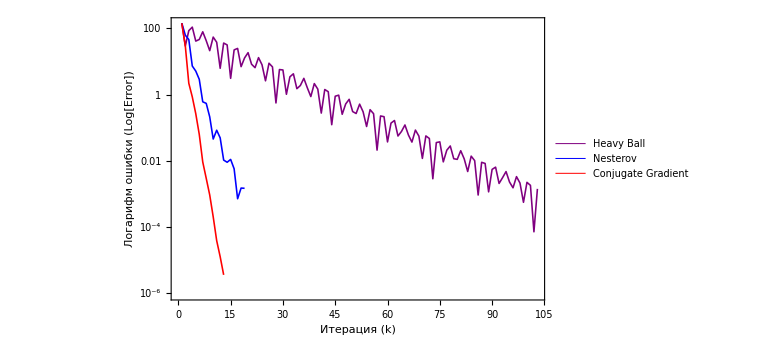

```mathematica
logsErrors = ListLogPlot[
{errorsBall, errorsNesterov, errorsGrads},
PlotStyle->{
Directive[Purple, Thickness[0.002]], 
Directive[Blue, Thickness[0.002]], 
Directive[Red, Thickness[0.002]]
},
Joined->True,
ImageSize->Large,
GridLines->Automatic,
Frame->True,
FrameLabel->{"Итерация (k)","Логарифм ошибки (Log[Error])"},
PlotLegends->Placed[{"Heavy Ball","Nesterov","Conjugate Gradient"},{Right,Top}]
]
(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/logsErrors.png",logsErrors,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

```mathematica
resultDecent = GradientDescentNumerical[f, x0, maxIter, tol];

xMinDecent = resultDecent[[1]];
trajectoryDecent=resultDecent[[2]];
errorsDecent = resultDecent[[3]];
```

Достигнута точность по норме градиента! Iter: 13

```mathematica
plotBall=ListPlot[
trajectoryBall,
PlotStyle->Directive[Red,PointSize[0.005], Thickness[0.003]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

plotNesterov=ListPlot[
trajectoryNesterov,
PlotStyle->Directive[Purple,PointSize[0.005], Thickness[0.003]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

plotDecent=ListPlot[
trajectoryDecent,
PlotStyle->Directive[Yellow,PointSize[0.005], Thickness[0.003]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

plotGrads=ListPlot[
trajectoryGrads,
PlotStyle->Directive[Blue,PointSize[0.005], Thickness[0.003]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"Aquamarine",PlotLabel->"General View"];

zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"Aquamarine",PlotLabel->"Zoomed View"];

show=Show[GraphicsRow[{
Show[generalPlot,plotDecent,plotBall, plotNesterov, plotGrads],
Show[zoomedPlot,plotDecent,plotBall, plotNesterov, plotGrads]}],
ImageSize->800];
```

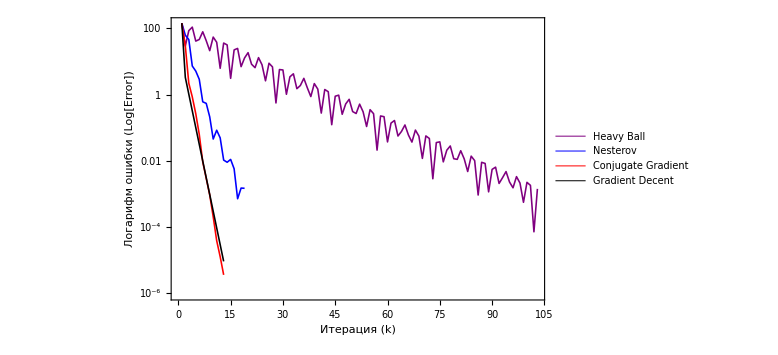

```mathematica
logsErrors = ListLogPlot[
{errorsBall, errorsNesterov, errorsGrads, errorsDecent},
PlotStyle->{
Directive[Purple, Thickness[0.002]], 
Directive[Blue, Thickness[0.002]], 
Directive[Red, Thickness[0.002]],
Directive[Black, Thickness[0.002]]
},
Joined->True,
ImageSize->Large,
GridLines->Automatic,
Frame->True,
FrameLabel->{"Итерация (k)","Логарифм ошибки (Log[Error])"},
PlotLegends->Placed[{"Heavy Ball","Nesterov","Conjugate Gradient", "Gradient Decent"},{Right,Top}]
]

Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/compareErrors15.png",logsErrors,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
```